-Graphics-

g1.png

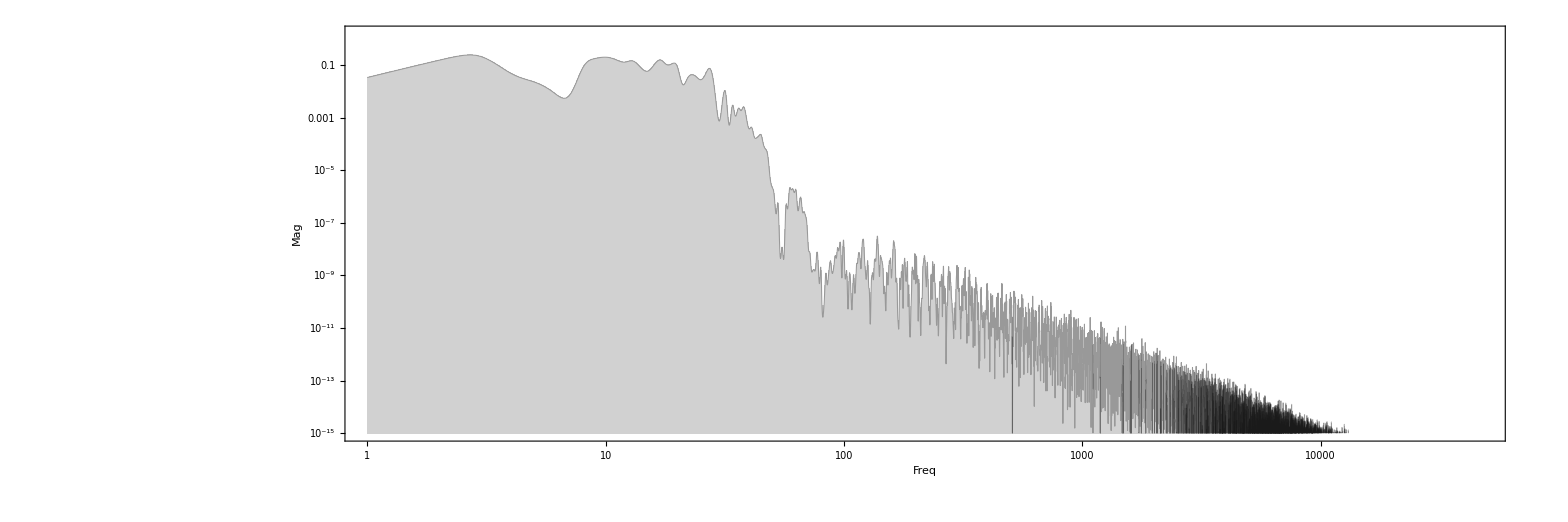

g2.png

```mathematica
ClearAll[n,signal,g1,g2];
SetDirectory[NotebookDirectory[]];

n=96000;
signal=RandomReal[{0,1},n];
g1=ListLogLogPlot[
PeriodogramArray[signal,n,512,HannWindow][[3;;]],
Filling->Axis,Joined->True,InterpolationOrder->3,
PlotStyle->Directive[GrayLevel[.3,.5],PointSize[Small],Thickness[0.0005]],
PlotRange->{{1,n/2},{10^-15,1.5}},
Frame->True,FrameLabel->{"Freq","Mag"},FrameStyle->Directive[Black,16],
AspectRatio->1/3,
ImageSize->2000,
PerformanceGoal->"Quality"]
Export["g1.png",g1,"PNG"]
g2=ListLogLogPlot[
PeriodogramArray[LowpassFilter[signal,Quantity[10,"Hertz"],SampleRate->48000],n,512,HannWindow][[3;;]],
Filling->Axis,Joined->True,InterpolationOrder->3,
PlotStyle->Directive[GrayLevel[.1,.3],PointSize[Small],Thickness[0.0005]],
PlotRange->{{1,n/2},{10^-15,1.5}},
Frame->True,FrameLabel->{"Freq","Mag"},FrameStyle->Directive[Black,16],
AspectRatio->1/3,
ImageSize->2000,
PerformanceGoal->"Quality"]
Export["g2.png",g2,"PNG"]
```